```mathematica
Integrate[Sqrt[1-x] / Sqrt[x] * Exp[-a^2 * x / 2], {x, 0, 1}]
```

1/2 ⅇ^(-a^2/4) π (BesselI[0,a^2/4]+BesselI[1,a^2/4])

```mathematica
?BesselI
```

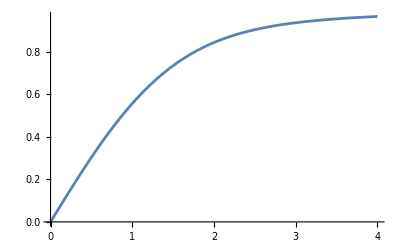

```mathematica
Plot[(1/2 ⅇ^(-a^2/4) π (BesselI[0,a^2/4]+BesselI[1,a^2/4])) * a / Sqrt[2 * Pi], {a, 0, 4}]
```

```mathematica
Integrate[Sqrt[1-x^2]  * Exp[-a^2 * x^2 / 2], {x, 0, 1}]
```

1/4 ⅇ^(-a^2/4) π (BesselI[0,a^2/4]+BesselI[1,a^2/4])

```mathematica
Integrate[Cos[x] (1/2) (1- k * r * Sin[x]), {x, 0, Pi/2}]
```

1/4 (2-k r)

```mathematica
Integrate[Cos[x]^2 * (1 / (1 + a^2 * Sin[x]^2)) / Pi, {x, 0, Pi/2}]
```

1/(2+2 √(1+a^2))

```mathematica
Cos[x]^2 * (1 / (1 + a^2 Sin[x]^2))
```

Cos[x]^2/(1+a^2 Sin[x]^2)